```mathematica
SetDirectory["/home/uyras/projects/partsEngine/build-PartsEngine-Desktop_Qt_5_4_0_GCC_64bit-Debug"];
```

```mathematica
(*Сохраняет в TIFF формате график посещенных энергий для каждого потока*)
energies = Union[ReadList["energies.txt"]];
ParallelTable[
Export["oe_"<>ToString[i]<>".tif",
data=ReadList["e_"<>ToString[i]<>".txt"];
dataLen=Length[data];
plot=Join[{data},Table[{{0,i},{dataLen,i}},{i,energies}]];
ListLinePlot[plot]
,"TIFF",ImageSize->1920
];,{i,0,49}
];
```

$Aborted

2.71828

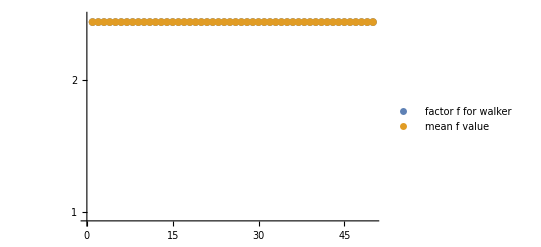

0 | 2.71828
1 | 2.71828
2 | 2.71828
3 | 2.71828
4 | 2.71828
5 | 2.71828
6 | 2.71828
7 | 2.71828
8 | 2.71828
9 | 2.71828
10 | 2.71828
11 | 2.71828
12 | 2.71828
13 | 2.71828
14 | 2.71828
15 | 2.71828
16 | 2.71828
17 | 2.71828
18 | 2.71828
19 | 2.71828
20 | 2.71828
21 | 2.71828
22 | 2.71828
23 | 2.71828
24 | 2.71828
25 | 2.71828
26 | 2.71828
27 | 2.71828
28 | 2.71828
29 | 2.71828
30 | 2.71828
31 | 2.71828
32 | 2.71828
33 | 2.71828
34 | 2.71828
35 | 2.71828
36 | 2.71828
37 | 2.71828
38 | 2.71828
39 | 2.71828
40 | 2.71828
41 | 2.71828
42 | 2.71828
43 | 2.71828
44 | 2.71828
45 | 2.71828
46 | 2.71828
47 | 2.71828
48 | 2.71828
49 | 2.71828

```mathematica
(* Выборка всех модификационных факторов из аналитики процесса*)
desc = OpenRead["analys.txt"];
Skip[desc,String];
data=Last/@ReadList[desc,Number,RecordLists->True];
mean = Mean[data](*Средний модификационный фактор*)
ListLogPlot[{data,Table[mean,{i,Length[data]}]},PlotRange->{0.95,2.8},PlotLegends->{"factor f for walker","mean f value"}]
Grid[Table[{i-1,data[[i]]},{i,1,Length[data]}],Frame->All]
```